# Flat surfae band

## Hamiltonian for Cu3PdN in the case of without spin-orbit coupling.

H = g0 σ_0+ gx σ_x + gz σ_z

where: g0=e0+A(kx^2+ ky^2+ kz^2);
gz=m0+B(kx^2+ ky^2+ kz^2);
gx=v kx ky kz;

Consider a surface terminated in z directoin. 
Supose the wave function has the form of Ψ=ϕ(k_x,k_y)e^(λ z). 
We have k_z→-ⅈ∂_z→-ⅈ λ;  k_z^2→-λ^2.
Fowllowing the method in SQ Shen and Bin Zhou's paper. We can calculate the surface states.

### Step I

By putting the trial wave function into Schrodinger equation  
[H(k_x,k_y,-ⅈ∂_z)-ξ]Ψ=0,  
the secular equation  
det[H(k_x,k_y,-ⅈ∂_z)-ξ]  
gives the solutions of λ(ξ).

```mathematica
Clear["Global`*"]

kx=k Cos[θ];
ky=k Sin[θ];

g0=e0+A(kx^2+ ky^2+(-λ^2));
gz=m0+B(kx^2+ ky^2+(-λ^2));
gx=v  kx ky(-ⅈ λ);

detH=FullSimplify[Det[(g0-ξ) PauliMatrix[0]+gx PauliMatrix[1]+gz PauliMatrix[3]]];
FullSimplify[detH];
λ=√X;
FullSimplify[sol=Solve[detH==0,X]];
(*Λ=λ^2*)


Λ1=FullSimplify[X/.sol[[1]]];
Λ2=FullSimplify[X/.sol[[2]]];

Em=(e0+A k^2)-(m0+B k^2);
Ep=(e0+A k^2)+(m0+B k^2);
F= A(e0+A k^2)-A ξ- B (m0+B k^2) -(k^2 v Sin[2 θ])^2/8;
T=(A-B) (A+B);

Λ1new=(F-√(F^2- T (Em-ξ)( Ep-ξ)))/T;
Λ2new=(F+√(F^2- T (Em-ξ)( Ep-ξ)))/T;
Print["Λ1-Λ1new =  ", FullSimplify[Λ1-Λ1new]]
Print["Λ2-Λ2new =  ", FullSimplify[Λ2-Λ2new]]
```

Λ1-Λ1new =  0

Λ2-Λ2new =  0

```mathematica
Clear["Global`*"]
Λ1new=(F-√(F^2- T (Em-ξ)( Ep-ξ)))/T;
Λ2new=(F+√(F^2- T (Em-ξ)( Ep-ξ)))/T;

Print["λ_1^2+λ_2^2 =  ", sum2=FullSimplify[Λ1new+Λ2new]]
Print["λ_1^2λ_2^2  =  ", prod2=FullSimplify[Λ1new Λ2new]]
```

λ_1^2+λ_2^2 =  (2 F)/T

λ_1^2λ_2^2  =  ((Em-ξ) (Ep-ξ))/T

### Step II

```mathematica
Clear["Global`*"]

H=g0 PauliMatrix[0]+gx PauliMatrix[1]+gz PauliMatrix[3];

{eig,vec}=Eigensystem[H];
{{eig[[1]],FullSimplify[vec[[1]]]},{ eig[[2]],FullSimplify[vec[[2]]]}}
```

{{g0-√(gx^2+gz^2),{(gz-√(gx^2+gz^2))/gx,1}},{g0+√(gx^2+gz^2),{(gz+√(gx^2+gz^2))/gx,1}}}

eig1 and vec1 lead to:     g0-√(gx^2+gz^2)=ξ;     √(gx^2+gz^2)=(g0-ξ)

eig2 and vec2 lead to:     g0+√(gx^2+gz^2)=ξ;     √(gx^2+gz^2)=(ξ-g0)

```mathematica
Clear["Global`*"]

CM1=gz1-(g01-ξ); CM2=gz2-(g02-ξ);
detCM=Det[{{CM1, CM2}, {gx1, gx2}}];

g01=e0+A(kx^2+ ky^2+ (-λ1^2));
gz1=m0+B(kx^2+ ky^2+ (-λ1^2));
gx1=v  kx ky(-ⅈ λ1);

g02=e0+A(kx^2+ ky^2+ (-λ2^2));
gz2=m0+B(kx^2+ ky^2+ (-λ2^2));
gx2=v  kx ky(-ⅈ λ2);

detCM=FullSimplify[detCM]
```

ⅈ kx ky v (λ1-λ2) (-e0+m0-(A-B) (kx^2+ky^2+λ1 λ2)+ξ)

```mathematica
Clear["Global`*"]
kx=k Cos[θ];
ky=k Sin[θ];
sol=Solve[(-e0+m0-(A-B) (kx^2+ky^2+λ12)+ξ)==0,λ12];
λ1λ2old=FullSimplify[λ12/.sol[[1]]];
λ1λ2=(ξ-Em)/(A-B);
Em=(e0+A k^2)-(m0+B k^2);
FullSimplify[λ1λ2old-λ1λ2]
```

0

```mathematica
Clear["Global`*"]
T=(A-B) (A+B);

prod=FullSimplify[(ξ-Em)/(A-B)];
prod2=FullSimplify[((Em-ξ) (Ep-ξ))/T];

FullSimplify[Solve[prod2-prod^2==0,ξ]]
```

{{ξ→Em},{ξ→(A (Em-Ep)+B (Em+Ep))/(2 B)}}

### Check and discusstion

Em=(e0+A k^2)-(m0+B k^2);
Ep=(e0+A k^2)+(m0+B k^2);
F= A(e0+A k^2)-A ξ- B (m0+B k^2) -(k^2 v Sin[2 θ])^2/8;
T=(A-B) (A+B);

```mathematica
Clear["Global`*"]

ξ=Em;
ξ=(A (Em-Ep)+B (Em+Ep))/(2 B);
Em=(e0+A k^2)-(m0+B k^2);
Ep=(e0+A k^2)+(m0+B k^2);
F= A(e0+A k^2)-A ξ- B (m0+B k^2) -(k^2 v Sin[2 θ])^2/8;
T=(A-B) (A+B);

Print["ξ =  ", FullSimplify[ξ]]

Λ1=(F-√(F^2- T (Em-ξ)( Ep-ξ)))/T;
Λ2=(F+√(F^2- T (Em-ξ)( Ep-ξ)))/T;

Print["λ_1^2λ_2^2  =  ", prod2=FullSimplify[Λ1 Λ2]]
Print["λ_1λ_2  =  ", prod2=FullSimplify[(ξ-Em)/(A-B)]]
Print["λ_1^2-λ_2^2 =  ", diff2=FullSimplify[Λ1-Λ2]]
Print["λ_1^2+λ_2^2 =  ", diff2=FullSimplify[Λ1+Λ2]]
Print["(λ_1+λ_2)^2 =  ", diff2=FullSimplify[Λ1+Λ2+2(ξ-Em)/(A-B)]]
Print["(λ_1-λ_2)^2 =  ", diff2=FullSimplify[Λ1+Λ2-2(ξ-Em)/(A-B)]]
```

ξ =  e0-(A m0)/B

λ_1^2λ_2^2  =  ((B k^2+m0)^2)/B^2

λ_1λ_2  =  -(B k^2+m0)/B

λ_1^2-λ_2^2 =  -(√((8 (A-B) (A+B) k^4 (B k^2+m0) v^2 (-1+Cos[4 θ]))/B+k^8 v^4 Sin[2 θ]^4))/(4 (A^2-B^2))

λ_1^2+λ_2^2 =  2 (k^2+m0/B)+(k^4 v^2 Cos[θ]^2 Sin[θ]^2)/(-A^2+B^2)

(λ_1+λ_2)^2 =  -(k^4 v^2 Cos[θ]^2 Sin[θ]^2)/(A^2-B^2)

(λ_1-λ_2)^2 =  4 (k^2+m0/B)+(k^4 v^2 Cos[θ]^2 Sin[θ]^2)/(-A^2+B^2)

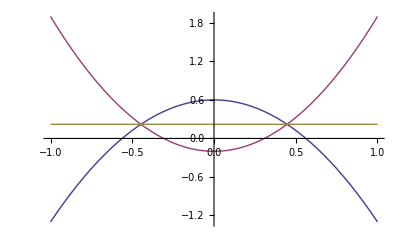

```mathematica
Clear["Global`*"]
A=0.1; B=2;m0=-0.4; v=0.2; e0=0.2;
Em=(e0+A k^2)-(m0+B k^2);
Ep=(e0+A k^2)+(m0+B k^2);
Ess=e0-(A m0)/B;
KX=1;
Plot[{Em,Ep,Ess},{k,-KX,KX}]
```

#### Plot

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
Lx=0.9;
Ly=Lx;
e0=0.0;

A=0.1; B=2;m0=-0.4; v=0.2; en=1;
ni=1;
figband1=ConstantArray[0,ni];figband2=ConstantArray[0,ni];

For[i=1,i<=ni,i++,
kz=0.75/ni*(i-1);
g0=e0+A(kx^2+ ky^2+ kz^2);
gz=m0+B(kx^2+ ky^2+ kz^2);
gx=v kx ky kz;
eigs=FullSimplify[Eigenvalues[g0 PauliMatrix[0]+gx PauliMatrix[1]+gz PauliMatrix[3]]];

figband1[[i]]=Plot3D[
{eigs[[1]]},{kx,-Lx,Lx},{ky,-Ly,Ly},Mesh->None,{PlotStyle->{Opacity[0.20],FaceForm[Red,Yellow]}} ];
figband2[[i]]=Plot3D[
{eigs[[2]]},{kx,-Lx,Lx},{ky,-Ly,Ly},Mesh->None,{PlotStyle->{Opacity[0.20],FaceForm[Blue,Yellow]}} ];
]

figNL=ParametricPlot3D[{Sin[θ] √(-m0/B),Cos[θ] √(-m0/B),e0-(A m0)/B},{θ,0,2π},PlotStyle->{Red,Thick,Thickness[0.0039]}];

flatband=FullSimplify[(e0-(A m0)/B)];
figflatband=Plot3D[flatband,{kx,-Lx,Lx},{ky,-Ly,Ly},Mesh->None,RegionFunction->Function[{kx,ky,z},B(kx^2+ky^2)<-m0-0.001],PlotStyle->{Opacity[0.55],FaceForm[Blue,Blue]}
];

gg=Show[{figband1,figband2,figNL,figflatband}, PlotRange->{{-Lx,Lx},{-Ly,Ly},{-en,en}},Axes->False,Boxed->False,AxesLabel->{"k_x","k_y",Rotate["Energy(eV)",90 Degree]},AxesStyle->{Directive[Blue,49],Directive[Blue,49],Directive[Blue,49]},
ViewVector->{{4,-4,3},{0,0,0}}]


Export["figs/flatband.png",gg,ImageSize->{350*4,200*4},Background->None]
```

-Graphics3D-

figs/flatband.png

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
Lx=0.5;
Lz=0.9;
e0=0.0;
A=0.0; B=2;m0=-0.4; v=0.2;
ni=390;
figband=ConstantArray[0,ni];
For[i=1,i<=ni,i++,
ky=kx;kz=0.48/ni*(i-1);
g0=e0+A( kx^2+ ky^2+kz^2); gz=m0+B( kx^2+ ky^2+ kz^2); gx=v kx ky kz;
eigs=FullSimplify[Eigenvalues[g0 PauliMatrix[0]+gx PauliMatrix[1]+gz PauliMatrix[3]]];

figband[[i]]=Plot[
{eigs[[1]],eigs[[2]]},{kx,-Lx,Lx},PlotStyle->{Black,Red,Thickness[0.0025]}
];]

en=0.0051;
gg=Show[{figband}, PlotRange->{{-Lx,Lx},{-en,en}},Axes->True,AxesLabel->{"k_x","Energy(eV)"},AxesStyle->{Directive[Black,9],Directive[Black,9]},Ticks->{{-0.05,0,0.05},{-0.4,0.4}}]

Export["flatband_kx.png",gg,ImageSize->{200*4,200*4},Background->None]
Export["../../latex/flatband_kx.png",gg,ImageSize->{200*4,200*4},Background->None]
```